```mathematica
Determining Se and Sm from the skyrmion field
```

```mathematica
R  = 1;
θ[r]:= π(1-Exp[-r^2/R^2]); (*Azimuthal angle*)
Integrate[2π r (Cos[θ[r]]+1),{r,0,Infinity}]
SeCoefficient=%//N
Sm = Integrate[2π r^2 Sin[θ[r]],{r,0,Infinity}]
SmCoefficient=%//N
```

π (EulerGamma-CosIntegral[π]+Log[π])

5.17822

∫_0^∞ 2 π r^2 Sin[(1-ⅇ^(-r^2)) π]ⅆr

6.53068

```mathematica
Simplify[∫_0^∞ 2 π r^2 Sin[(1-ⅇ^(-r^2)) π]ⅆr]
```

∫_0^∞ 2 π r^2 Sin[ⅇ^(-r^2) π]ⅆr

{-1.14109,-1.14109,1.14109,1.14109}

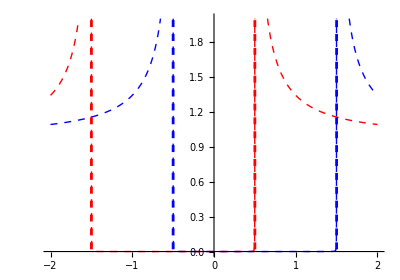

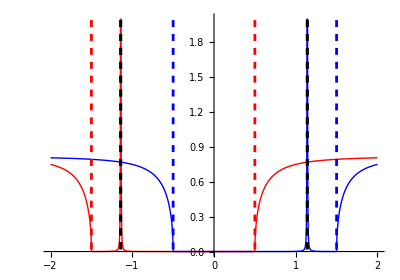

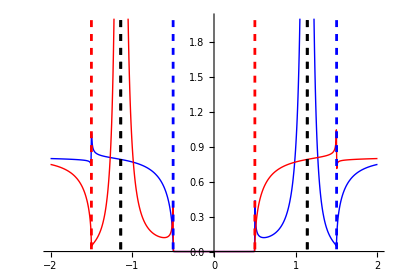

```mathematica
Plotting  LDOS near the skyrmion ;
id =({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});σx=({{0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}}) ; σy=({{0, -ⅈ, 0, 0}, {ⅈ, 0, 0, 0}, {0, 0, 0, -ⅈ}, {0, 0, ⅈ, 0}}); σz =({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, -1}}); τx = ({{0, 0, 1, 0}, {0, 0, 0, 1}, {1, 0, 0, 0}, {0, 1, 0, 0}}); τz =({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});
EF = 1; p =1; ρ= 1/(4π);  (*Fermi energy and momentum fix DOS*)
Δ = 0.25 EF;S = 0.5Δ;  (*Gap and external magnetization*)
R =1.7;  Se =  R^2 S SeCoefficient; Sm = 0.1 R^3 S SmCoefficient;(*Parameters of skyrmion: size and effective out-of-plane spin, effective in-plane monopole moment*)

 X =Se π ρ;  ES =  (1-X^2)/(1+X^2);  (*position of conventional YSR state*)
Γ= 0.00001; (*imaginary infinitesimal*)
ClearAll["ω","LDOS","G","barG"]

G[ω_]:=-π ρ ((id+σz)/2) .(((ω+ⅈ Γ-S)id +Δ τx)/(√(Δ^2-(ω+ⅈ Γ-S)^2)))-π ρ ((id-σz)/2) .(((ω+ⅈ Γ+S)id +Δ τx)/(√(Δ^2-(ω+ⅈ Γ+S)^2)));
barG[ω_]:= -π ρ ((id-σz)/2) .(((ω+ⅈ Γ-S)id +Δ τx)/(√(Δ^2-(ω+ⅈ Γ-S)^2)))-π ρ ((id+σz)/2) .(((ω+ⅈ Γ+S)id +Δ τx)/(√(Δ^2-(ω+ⅈ Γ+S)^2)));
T[ω_]:=Inverse[id+Se σz.G[ω]-Sm^2 p^2 G[ω].barG[ω]].(-Se σz+Sm^2 p^2 barG[ω]);
T0[ω_]:=Inverse[id+Se σz.G[ω]].(-Se σz);

LDOSσ[ω_,σ_]:= -1/π Im[Tr[((id+τz)/2).((id+σ)/2).(G[ω]+G[ω].T[ω].G[ω])]];
LDOSσ0[ω_,σ_]:= -1/π Im[Tr[((id+τz)/2).((id+σ)/2).(G[ω]+G[ω].T0[ω].G[ω])]];
LDOSσAwayFromSkyrmion[ω_,σ_]:= -1/π Im[Tr[((id+τz)/2).((id+σ)/2).G[ω]]];


Solution for the  T-matrix poles;


ClearAll["ω","g","barg"]
g=-π ρ ((id+σz)/2) .(((ω-S)id +Δ τx)/(√(Δ^2-(ω-S)^2)))-π ρ ((id-σz)/2) .(((ω+S)id +Δ τx)/(√(Δ^2-(ω+S)^2)));
barg  = -π ρ ((id-σz)/2) .(((ω-S)id +Δ τx)/(√(Δ^2-(ω-S)^2)))-π ρ ((id+σz)/2) .(((ω+S)id +Δ τx)/(√(Δ^2-(ω+S)^2)));
(*Find determinant and find roots*)
ListOfTmatrixPoles=(ω/.Solve[ Simplify[Det[id+Se σz.g]]==0,ω])/Δ//Re 

Preparation before plotting ;

maxY = 2; (* PlotRange/.AbsoluteOptions[gr1,PlotRange] //Flatten//Last;*)
VerticalLine [ω_] :=Line[{{ω,-0.1},{ω,maxY +0.1}}]; (*define auxiliarly function*)
aspRatio = 0.7;




Plot LDOS for pure ferromagnet ;
gr1 = Plot[{LDOSσAwayFromSkyrmion[Δ ω,σz]/ρ,LDOSσAwayFromSkyrmion[Δ ω,-σz]/ρ},{ω,-2,2},PlotStyle->{{Thick,Dashed,Blue},{Thick, Dashed,Red}},
TicksStyle-> Directive[18],AspectRatio->0.7,PlotRange->{{-2,2},{0,maxY}}];
gr1a = Graphics[{Blue,Dashed,Thickness[0.005],VerticalLine /@ {1+S/Δ,-1+S/Δ},Red,VerticalLine /@ {1-S/Δ,-1-S/Δ}}];
Show[gr1,gr1a]

Plot LDOS for skyrmion with simple T-matrix     ;
gr2 = Plot[{LDOSσ0[Δ ω,σz]/ρ,LDOSσ0[Δ ω,-σz]/ρ},{ω,-2,2},PlotStyle->{{Thick,Blue},{Thick, Red},{Thick,Blue,Thickness[0.005],Dashing[0.05]},{Thick, Red,Thickness[0.005],Dashing[0.05]},{Thick, Black},{Thickness[0.01],Dashing[0.05],Green//Darker}},
TicksStyle-> Directive[18],AspectRatio->aspRatio,PlotRange->{{-2,2},{0,maxY}},MaxRecursion->6];
gr2a = Graphics[{Blue,Dashed,Thickness[0.005],VerticalLine /@ {1+S/Δ,-1+S/Δ},Red,VerticalLine /@ {1-S/Δ,-1-S/Δ},Black,VerticalLine/@ ListOfTmatrixPoles}];
Show[gr2,gr2a]

Plot LDOS for skyrmion with modified T-matrix     ;

gr3 = Plot[{LDOSσ[Δ ω,σz]/ρ,LDOSσ[Δ ω,-σz]/ρ},{ω,-2,2},PlotStyle->{{Thick,Blue},{Thick, Red},{Thick, Black},{Thickness[0.01],Dashing[0.05],Green//Darker}},
TicksStyle-> Directive[18],AspectRatio->aspRatio,PlotRange->{{-2,2},{0,maxY}},MaxRecursion->4];

Show[gr3,gr2a]
```

```mathematica
u
```

```mathematica
N[1/(2π)]
```

```mathematica
E
```

```mathematica
Integrate[Sin[x]/x,{x,0,Infinity}]
Integrate[Sin[x]/x Sin[x/3]/(x/3),{x,0,Infinity}]
Integrate[Sin[x]/x Sin[x/3]/(x/3)Sin[x/5]/(x/5),{x,0,Infinity}]
Integrate[Sin[x]/x Sin[x/3]/(x/3)Sin[x/5]/(x/5)Sin[x/6]/(x/6),{x,0,Infinity}]

Integrate[Sin[x]/x Sin[x/3]/(x/3)Sin[x/5]/(x/5)Sin[x/7]/(x/7)Sin[x/9]/(x/9)Sin[x/11]/(x/11)Sin[x/13]/(x/13)Sin[x/15]/(x/15),{x,0,Infinity}]
```

π/2

π/2

π/2

«1 more identical outputs»

(467807924713440738696537864469 π)/935615849440640907310521750000

```mathematica
1/3+1/5+1/7+1/9+1/11+1/13+1/15
```

46027/45045

```mathematica
FullSimplify[Integrate[(Cos[a Cos[ϕ]]Exp[ - b Cos[ϕ]])/(2 π),{ϕ,-π/2,π/2}, Assumptions->a>0&&b>0]]
```

Integrate[(ⅇ^(-b Cos[ϕ]) Cos[a Cos[ϕ]])/(2 π),{ϕ,-π/2,π/2},Assumptions→a>0&&b>0]

```mathematica
Integrate[(Exp[(ⅈ  a - b)  Sin[ϕ]]-Exp[(-ⅈ  a - b)  Sin[ϕ]])/(2π),{ϕ,0,π},Assumptions-> a>0 && b>0]
```

1/2 (-BesselJ[0,a-ⅈ b]+BesselJ[0,a+ⅈ b]+ⅈ StruveH[0,a-ⅈ b]+ⅈ StruveH[0,a+ⅈ b])

```mathematica
1/2 (BesselJ[0,a-ⅈ b]+BesselJ[0,a+ⅈ b]-ⅈ StruveH[0,a-ⅈ b]+ⅈ StruveH[0,a+ⅈ b])
```

```mathematica
%//FullSimplify
```

```mathematica
f[a_,b_]:=1/2 (BesselJ[0,(pF-ⅈ pX)/x]+BesselJ[0,(pF+ⅈ pX)/x]-ⅈ StruveH[0,(pF-ⅈ pX)/x]+ⅈ StruveH[0,(pF+ⅈ pX)/x]);
Expand
```

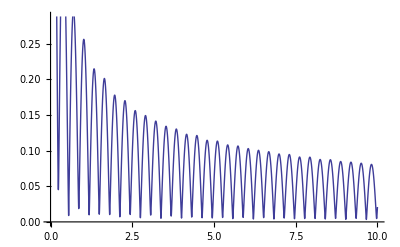

```mathematica
Plot[Abs[N[f[10x,ⅈ x]]],{x,0,10}]
```

```mathematica
Series[1/2 (BesselJ[0,(pF-ⅈ pX)x]+BesselJ[0,(pF+ⅈ pX)x]-ⅈ StruveH[0,(pF-ⅈ pX)x]+ⅈ StruveH[0,(pF+ⅈ pX)x]),{x,Infinity,0},Assumptions -> {pF>0 && pX>0}]
```

```mathematica
Cos[pF x-ⅈ pX x] ((ⅈ √(1/x))/(2 √π √(pF-ⅈ pX))+O[1/x]^(3/2))+Cos[π/4-pF x+ⅈ pX x] ((√(1/x))/(√(2 π) √(pF-ⅈ pX))+O[1/x]^(3/2))+Cos[pF x+ⅈ pX x] (-(ⅈ √(1/x))/(2 √π √(pF+ⅈ pX))+O[1/x]^(3/2))+Cos[π/4+pF x+ⅈ pX x] ((ⅈ √(1/x))/(√(2 π) √(pF+ⅈ pX))+O[1/x]^(3/2))+(-(ⅈ √(1/x))/(2 √π √(pF-ⅈ pX))+O[1/x]^(3/2)) Sin[pF x-ⅈ pX x]+((ⅈ √(1/x))/(2 √π √(pF+ⅈ pX))+O[1/x]^(3/2)) Sin[pF x+ⅈ pX x]
```

```mathematica
FullSimplify[NIntegrate[Tanh[ ξ ]/ξ,{ξ,0,Infinity}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::zeroregion: Integration region {{0., 0}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ξ near {ξ} = {8.1933649966303075080653271703138185060184363358617443426489735027×10^-76}. NIntegrate obtained -224.507 and 6.91047 for the integral and error estimates.

```mathematica
Integrate[1/(√(Δ^2+(x-S)^2)),{x,-Subscript[ω, D],Subscript[ω, D]},Assumptions-> Subscript[ω, D]>0&& Δ>0&&S>0]
```

Log[(S+ω_D+√(S^2+Δ^2+2 S ω_D+ω_D^2))/(S-ω_D+√(S^2+Δ^2-2 S ω_D+ω_D^2))]

```mathematica
Integrate[x/(√(1+x^2)),{x,0,A},Assumptions -> A>0]
```

-1+√(1+A^2)

```mathematica
Integrate[x/(√(1-x^2)),{x,0,1},Assumptions -> A>0]
```

1

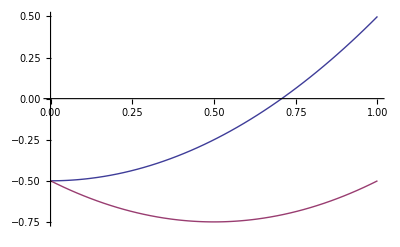

```mathematica
Plot[{-1/2+S^2,-1/2+S^2-S},{S,0,1}]
```

```mathematica
Integrate[ⅇ^(+ⅈ x Cos[ϕ]- y √((Cos[2ϕ]+1)/2)),{ϕ,-π,π},Assumptions-> {x>0&&y>0}]//FullSimplify
```

π (BesselJ[0,x-ⅈ y]+BesselJ[0,x+ⅈ y]-ⅈ StruveH[0,x-ⅈ y]+ⅈ StruveH[0,x+ⅈ y])

```mathematica
Integrate[ⅇ^(-y ()) Cos[x Cos[ϕ]],{ϕ,-π,π},Assumptions->x>0&&y>0]
```

2 π BesselJ[0,x-ⅈ y]

```mathematica
FullSimplify[StruveH[0,ⅈ x+ⅈ y], Assumptions-> {x>0&& y>0}]
```

ⅈ StruveL[0,x+y]

```mathematica
Integrate[BesselJ[0,x]/((x-p)^2+Δ^2),{x,-Infinity,Infinity},Assumptions-> {p>0&& Δ>0}]
Series[(π (BesselJ[0,p-ⅈ Δ]+BesselJ[0,p+ⅈ Δ]-ⅈ StruveH[0,p-ⅈ Δ]+ⅈ StruveH[0,p+ⅈ Δ]))/(2 Δ),{p,Infinity,1}]//FullSimplify
```

```mathematica
O[1/p]^2+((ⅇ^-Δ √π √(1/p))/Δ+O[1/p]^(3/2)) (Cos[p]+Sin[p])
```

```mathematica
Integrate[(x-p)BesselJ[0,x]/((x-p)^2+Δ^2),{x,-Infinity,Infinity},Assumptions-> {p>0&& Δ>0}]
Series[%,{p,Infinity,1}]//FullSimplify
```

-1/2 ⅈ π (BesselJ[0,p-ⅈ Δ]-BesselJ[0,p+ⅈ Δ]-ⅈ StruveH[0,p-ⅈ Δ]-ⅈ StruveH[0,p+ⅈ Δ])

```mathematica
-Cosh[Δ]+Sinh[Δ]//FullSimplify
```

-Cosh[Δ]+Sinh[Δ]

```mathematica
Series[BesselJ[0,x],{x,0,4}]
```

1-x^2/4+x^4/64+O[x]^5

```mathematica
F[x_]:=Integrate[Exp[-x √(1+ω^2+ⅈ ω/4)]/(2π),{ω,-Infinity,Infinity}]//N;
```

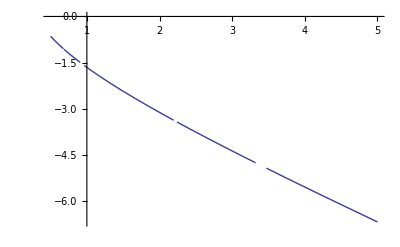

```mathematica
Plot[Log[F[x]],{x,0.5,5}]
```

```mathematica
F[1]
```

0.190552+0. ⅈ

```mathematica
Integrate[Cos[x]/(√(x^2+a^2)+b^2),{x,-Infinity,Infinity},Assumptions-> {a>0 && b>0}]//FullSimplify
```

```mathematica
Integrate[Cos[x]/(b^2+√(a^2+x^2)),{x,-∞,∞},Assumptions->a>0&&b>0]
```

```mathematica
j=1;
H= ConstantArray[0,{2*L,2*L}];
Subscript[S, 1]=0;

For[i=1,i<L+1,i++,
	H[[2i-1]][[2i-1]]=S;                   
	H[[2i]][[2i]]=-S; 

 
i1 = Mod[i,L]+1;
          H[[2i-1]][[2i1-1]]=1;
	H[[2i1-1]][[2i-1]]=1;
          H[[2i1]][[2i]]=1;
          H[[2i]][[2i1]]=1;

            ];

(*Remove circular boundary conditions
H[[1]][[2L-1]]=0;
H[[2]][[2L]]=0;
H[[2L-1]][[1]]=0;
H[[2L]][[2]]=0; *)



(*Define impurity in the center of the chain at j = L/2*)
H[[L-1]][[L-1]] = Subscript[S, 0];
H[[L]][[L]] = -Subscript[S, 0];
H[[L-1]][[L]] = Subscript[S, 1];
H[[L]][[L-1]] = Subscript[S, 1];

(*Define impurity at the x = j *)
H[[2*j-1]][[2*j-1]]=Subscript[S, 0];
H[[2*j]][[2*j]]=-Subscript[S, 0];
H[[2*j-1]][[2*j]] = Subscript[S, 1];
H[[2*j]][[2*j-1]] = Subscript[S, 1]; 

eigVals = Eigenvalues[H];
groundStateEnergy = HeavisideTheta[-eigVals].eigVals;
```

```mathematica
groundStateEnergy0 = groundStateEnergy;
```

```mathematica
groundStateEnergy
```

-1314.42

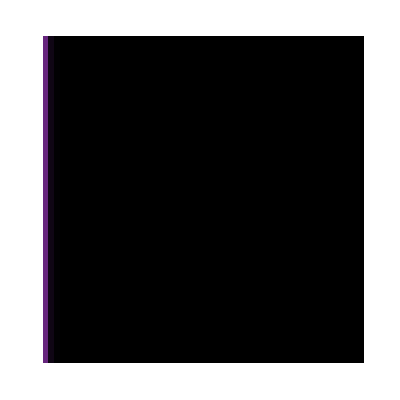

-Graphics-

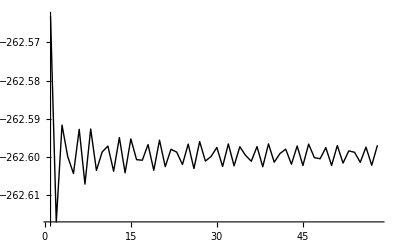

```mathematica
L =200; (*System size*) 

S = 0.5;
Subscript[S, 0] = -1.5*0; 
Subscript[S, 1] =-0.3*0;

(*Projectors onto spin-up and spin-down subbands*)
Pup = ConstantArray[0,{2*L,2*L}];
Pdown = ConstantArray[0,{2*L,2*L}];
For[i=1,i<L+1,i++,
	Pup[[2i-1]][[2i-1]]=1;                   
	Pdown[[2i]][[2i]]=1; ];

Matrix={}; (*Matrix of DOS*)
groundStateEnergy = {}; (*Matrix of DOS*)


Monitor[For[j=2,j<60,j=j+1,




H= ConstantArray[0,{2*L,2*L}];


For[i=1,i<L+1,i++,
	H[[2i-1]][[2i-1]]=S;                   
	H[[2i]][[2i]]=-S; 

 
i1 = Mod[i,L]+1;
          H[[2i-1]][[2i1-1]]=1;
	H[[2i1-1]][[2i-1]]=1;
          H[[2i1]][[2i]]=1;
          H[[2i]][[2i1]]=1;

            ];

(*Remove circular boundary conditions
H[[1]][[2L-1]]=0;
H[[2]][[2L]]=0;
H[[2L-1]][[1]]=0;
H[[2L]][[2]]=0; *)



(*Define impurity in the center of the chain at j = L/2*)
H[[1]][[1]] = Subscript[S, 0];
H[[2]][[2]] = -Subscript[S, 0];
H[[1]][[2]] = Subscript[S, 1];
H[[2]][[1]] = Subscript[S, 1];

(*Define impurity at the x = j *)
H[[2*j-1]][[2*j-1]]=Subscript[S, 0];
H[[2*j]][[2*j]]=-Subscript[S, 0];
H[[2*j-1]][[2*j]] = Subscript[S, 1];
H[[2*j]][[2*j-1]] = Subscript[S, 1]; 



δ = 0.002;
energyMesh = 0.06;
EnergyWindow = Table[e,{e,-3,-3,-energyMesh }];
(*
energyMesh = 0.001;
EnergyWindow = Table[e,{e,-2.2,-2.5,-energyMesh }]; *)


DOS = ConstantArray[0,Length[EnergyWindow]];
LDOSSpinUp = ConstantArray[0,Length[EnergyWindow]];
LDOSSpinDown = ConstantArray[0,Length[EnergyWindow]];
DOSUp = ConstantArray[0,Length[EnergyWindow]];
DOSDown = ConstantArray[0,Length[EnergyWindow]];
eignVecs = Eigenvectors[H];

(*Calculate ground state energy*)
eigVals = Eigenvalues[H];
groundStateEnergy = Append[groundStateEnergy,HeavisideTheta[-eigVals].eigVals];

For[i=1,i<2L+1,i++,
    Psi = eignVecs[[i]];
    ϵ  = Psi*.H.Psi;
  (*  Print[ϵ]; *)
 DOS =DOS+ (*Abs[SpinUp.Psi]^2*)δ/((ϵ-EnergyWindow)^2+δ^2);
LDOSSpinUp =LDOSSpinUp+Abs[Psi[[1]]]^2 δ/((ϵ-EnergyWindow)^2+δ^2);
LDOSSpinDown =LDOSSpinDown+Abs[Psi[[2]]]^2 δ/((ϵ-EnergyWindow)^2+δ^2);
 DOSUp = DOSUp + Psi.Pup.Psi δ/((ϵ-EnergyWindow)^2+δ^2);
 DOSDown = DOSDown + Psi.Pdown.Psi δ/((ϵ-EnergyWindow)^2+δ^2); 
]
(*DOS = DOS;*)
  Matrix = Append[Matrix,DOSUp];

],ProgressIndicator[j/100]];
ArrayPlot[Matrixᵀ ,ColorFunction->"SunsetColors",AspectRatio->1]

ListPlot[{{EnergyWindow,DOS}ᵀ,{EnergyWindow,LDOSSpinUp }ᵀ},Joined->True,PlotStyle->{{Black},{Blue,Thick}},PlotRange->All]
ListPlot[groundStateEnergy,Joined->True,PlotStyle->{{Black}},PlotRange->All]
```

```mathematica
LDOSSpinUp
```

{0.000966588 Abs[{-0.348237,1.16573×10^-15,«396»,0.271895,2.39491×10^-16}[1]]^2+0.000966588 Abs[{-0.348234,«398»,«24»}[1]]^2+«396»+0.000287236 Abs[«1»]^2+0.000138278 Abs[{0.0973168,«398»,3.0182×10^-16}[1]]^2}

```mathematica
ListPlot[LDOSSpinUp,Joined->True,PlotStyle->{{Blue,Thick},{Red,Thick}},PlotRange->All]
```

-Graphics-

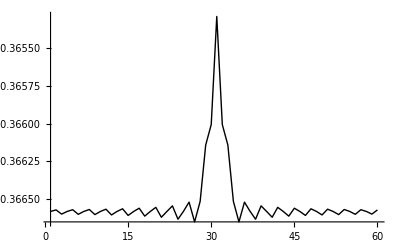

```mathematica
groundStateEnergyA= groundStateEnergy;
```

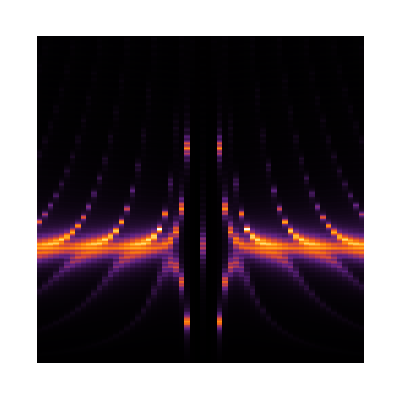

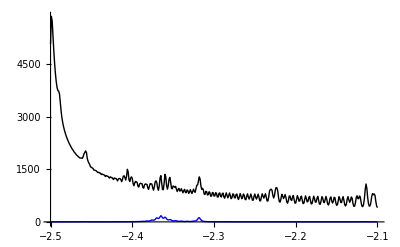

```mathematica
ListPlot[{groundStateEnergyF,groundStateEnergyA},Joined->True,PlotStyle->{Red,Blue,Green},PlotRange->All]
```

```mathematica
Manipulate[ListPlot[Matrix[[j]],Joined->True,PlotStyle->{{Black},{Blue,Thick}},PlotRange->{0,250}],{j,10,Matrix//Length,1}]
```

Part::partw: Part 10 of {DOSup, DOSup, DOSup} does not exist.

ListPlot::lpn: {DOSup, DOSup, DOSup} ⟦ 10 ⟧ is not a list of numbers or pairs of numbers.

```mathematica
u
```

```mathematica
EnergyWindow//Length
```

```mathematica
{1,2}.{3,4}
counter ++
```

11

Increment::rvalue: counter is not a variable with a value, so its value cannot be changed.

```mathematica
counter++;
```

Increment::rvalue: counter is not a variable with a value, so its value cannot be changed.

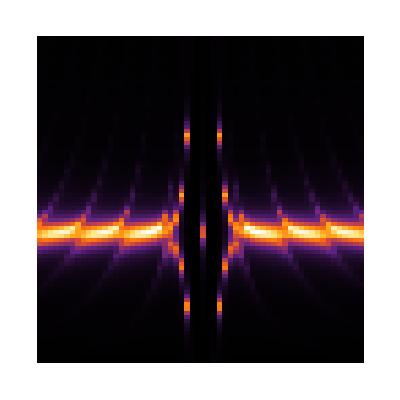

```mathematica
ListPlot[Matrix.EnergyWindow,Joined->True,PlotStyle->{{Black},{Blue,Thick}},PlotRange->Automatic]
```

```mathematica
{{1,2},{3,4}}.{x,y}
```

{x+2 y,3 x+4 y}

```mathematica
Abs[{-2,-1}]
```

{2,1}

```mathematica
L = 1000;
j=500;
Subscript[S, 1] = 0.7;
H= ConstantArray[0,{2*L,2*L}];


For[i=1,i<L+1,i++,
	H[[2i-1]][[2i-1]]=S;                   
	H[[2i]][[2i]]=-S; 

 
i1 = Mod[i,L]+1;
          H[[2i-1]][[2i1-1]]=1;
	H[[2i1-1]][[2i-1]]=1;
          H[[2i1]][[2i]]=1;
          H[[2i]][[2i1]]=1;

            ];

(*Remove circular boundary conditions
H[[1]][[2L-1]]=0;
H[[2]][[2L]]=0;
H[[2L-1]][[1]]=0;
H[[2L]][[2]]=0; *)


(*Define impurity in the center of the chain at j = L/2*)
H[[1]][[1]] = Subscript[S, 0];
H[[2]][[2]] = -Subscript[S, 0];
H[[1]][[2]] = Subscript[S, 1];
H[[2]][[1]] = Subscript[S, 1];

(*Define impurity at the x = j *)
H[[2*j-1]][[2*j-1]]=Subscript[S, 0];
H[[2*j]][[2*j]]=-Subscript[S, 0];
H[[2*j-1]][[2*j]] = Subscript[S, 1];
H[[2*j]][[2*j-1]] = Subscript[S, 1]; 

eigVals = Eigenvalues[H];
HeavisideTheta[-eigVals].eigVals
```

```mathematica
-1314.574257277195
```

-1314.57

```mathematica
-1314.5739389572404
```

-1314.57

```mathematica
-1314.4245220909997
```

-1314.42

```mathematica
-1314.4243621661624
```

-1314.42

```mathematica
Integrate[ⅈ/(x^2 ⅇ^(ⅈ α)+1),{x,-Infinity,Infinity},Assumptions->α>0]//FullSimplify
```

(ⅈ π)/(√(ⅇ^(ⅈ α)))

```mathematica
L =200; (*System size*) 

S = 0.5;
Subscript[S, 0] = -1.5*0; 
Subscript[S, 1] =-0.3*0;
j=L/2;

(*Projectors onto spin-up and spin-down subbands*)
Pup = ConstantArray[0,{2*L,2*L}];
Pdown = ConstantArray[0,{2*L,2*L}];
For[i=1,i<L+1,i++,
	Pup[[2i-1]][[2i-1]]=1;                   
	Pdown[[2i]][[2i]]=1; ];

Matrix={}; (*Matrix of DOS*)
groundStateEnergy = {}; (*Matrix of DOS*)
```

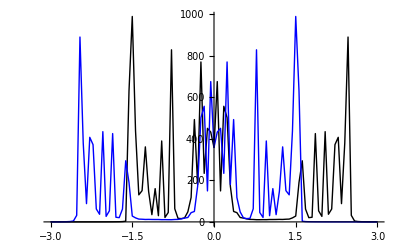

```mathematica
H= ConstantArray[0,{2*L,2*L}];


For[i=1,i<L+1,i++,
	H[[2i-1]][[2i-1]]=S;                   
	H[[2i]][[2i]]=-S; 

 
i1 = Mod[i,L]+1;
          H[[2i-1]][[2i1-1]]=1;
	H[[2i1-1]][[2i-1]]=1;
          H[[2i1]][[2i]]=1;
          H[[2i]][[2i1]]=1;

            ];



(*Define impurity in the center of the chain at j = L/2*)
H[[1]][[1]] = Subscript[S, 0];
H[[2]][[2]] = -Subscript[S, 0];
H[[1]][[2]] = Subscript[S, 1];
H[[2]][[1]] = Subscript[S, 1];

(*Define impurity at the x = j *)
H[[2*j-1]][[2*j-1]]=Subscript[S, 0];
H[[2*j]][[2*j]]=-Subscript[S, 0];
H[[2*j-1]][[2*j]] = Subscript[S, 1];
H[[2*j]][[2*j-1]] = Subscript[S, 1]; 



δ = 0.002;
energyMesh = 0.06;
EnergyWindow = Table[e,{e,3,-3,-energyMesh }];
(*
energyMesh = 0.001;
EnergyWindow = Table[e,{e,-2.2,-2.5,-energyMesh }]; *)


DOS = ConstantArray[0,Length[EnergyWindow]];
LDOSSpinUp = ConstantArray[0,Length[EnergyWindow]];
LDOSSpinDown = ConstantArray[0,Length[EnergyWindow]];
DOSUp = ConstantArray[0,Length[EnergyWindow]];
DOSDown = ConstantArray[0,Length[EnergyWindow]];
eignVecs = Eigenvectors[H];

(*Calculate ground state energy*)
eigVals = Eigenvalues[H];
groundStateEnergy = Append[groundStateEnergy,HeavisideTheta[-eigVals].eigVals];

For[i=1,i<2L+1,i++,
    Psi = eignVecs[[i]];
    ϵ  = Psi*.H.Psi;
  (*  Print[ϵ]; *)
 DOS =DOS+ (*Abs[SpinUp.Psi]^2*)δ/((ϵ-EnergyWindow)^2+δ^2);
LDOSSpinUp =LDOSSpinUp+Abs[Psi[[1]]]^2 δ/((ϵ-EnergyWindow)^2+δ^2);
LDOSSpinDown =LDOSSpinDown+Abs[Psi[[2]]]^2 δ/((ϵ-EnergyWindow)^2+δ^2);
 DOSUp = DOSUp + Psi.Pup.Psi δ/((ϵ-EnergyWindow)^2+δ^2);
 DOSDown = DOSDown + Psi.Pdown.Psi δ/((ϵ-EnergyWindow)^2+δ^2); 
]
ListPlot[{{EnergyWindow,DOSUp}ᵀ,{EnergyWindow,DOSDown }ᵀ},Joined->True,PlotStyle->{{Black},{Blue,Thick}},PlotRange->All]
```